```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
readMat[n_]:=Module[
{matData,stream,filename},
filename=StringJoin["matrix",ToString[n],".txt"];
stream=OpenRead[filename];
matData=Table[
Skip[stream,Word];
Read[stream,Number]
,{65959}];
Close[stream];
matData
]
(*larry =  Plot[fitline, {x, 0, 10}];*)
allData=Table[readMat[i],{i,0,10}];
lm= LinearModelFit[Transpose[allData][[1]], { x,x^2}, x];
maxResiduals=Table[
NotebookDelete[temp];
temp=PrintTemporary[i];
lm= LinearModelFit[Transpose[allData][[i]], { x,x^2}, x];
Max[lm["FitResiduals"]^2]
,{i,Length[Transpose[allData]]}];
```

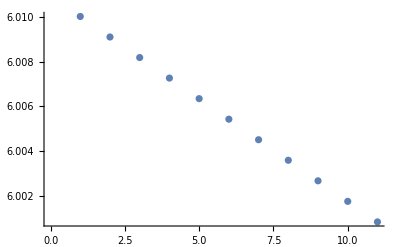

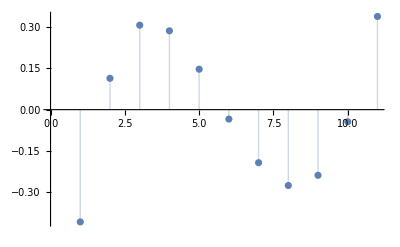

0.165684

{{36239},{40415},{47750},{65750}}

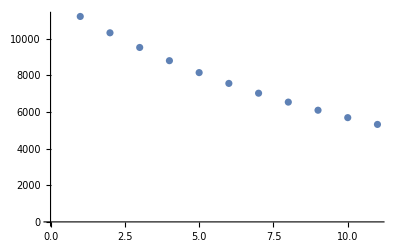

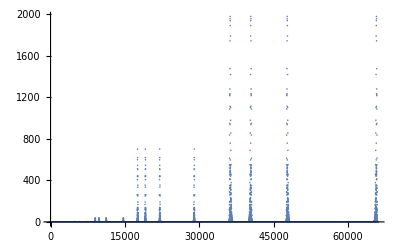

```mathematica
Show[
ListPlot[Transpose[allData][[1]]],
Plot[lm[x],{x,0,11}]]
ListPlot[lm["FitResiduals"],Filling->Axis]
Max[lm["FitResiduals"]^2]
(*Print[maxResiduals]*)
Position[maxResiduals, Max[maxResiduals]]
ListPlot[Transpose[allData][[40415]]]
ListPlot[maxResiduals, PlotRange->All]
```